```mathematica
SetDirectory[NotebookDirectory[]];
<<MeshTools.wl
```

```mathematica
bmesh=BoundaryElementMeshJoin[ToBoundaryMesh[Rectangle[{-3,-1},{3,1}]],ToBoundaryMesh[Circle[{0,0},10]]]
```

BoundaryElementMeshJoin[ToBoundaryMesh[Rectangle[{-3,-1},{3,1}]],ToBoundaryMesh[Circle[{0,0},10]]]

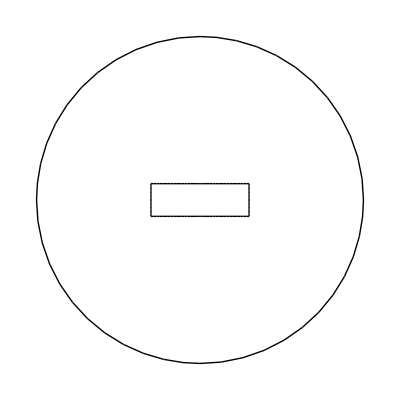

```mathematica
bmesh["Wireframe"]
```

```mathematica
mesh=ToElementMeshDefault[bmesh,{{{0,0},2},{{2,2},1}}]
```

ElementMesh[{{-10.,10.},{-10.,10.}},{TriangleElement[<1274>]}]

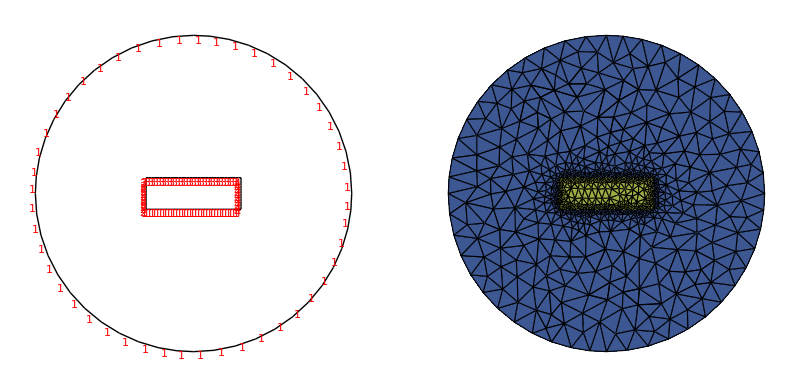

```mathematica
MeshInspect[mesh]
```

```mathematica
pde=Laplacian[a[x,y],{x,y}]==Piecewise[{{(y,{x,y}∈Rectangle[{-3,-1},{3,1}]}},0];
bcs=DirichletCondition[a[x,y]==0,x^2+y^2≥100];
```

```mathematica
A=NDSolveValue[{pde,bcs},a,{x,y}∈mesh]
```

InterpolatingFunction[…]

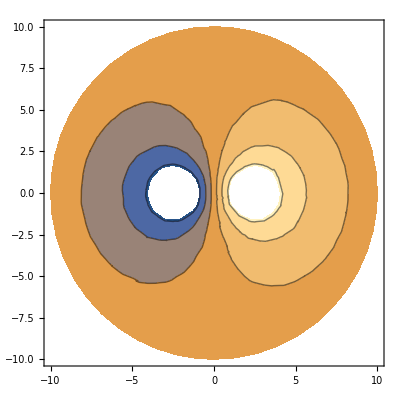

```mathematica
ContourPlot[A[x,y],{x,y}∈mesh]
```

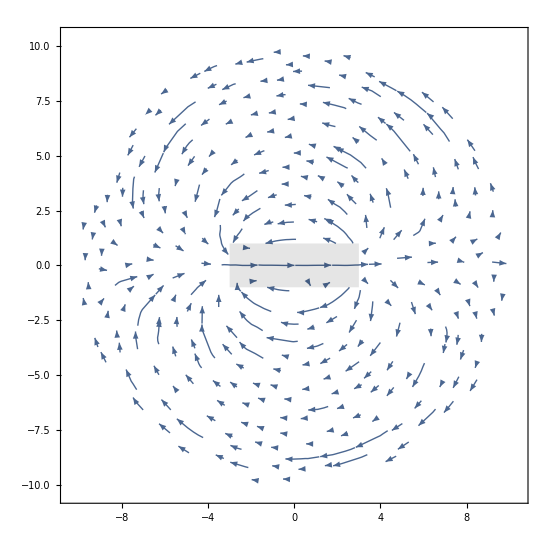

```mathematica
Show[StreamPlot[Evaluate[Curl[A[x,y],{x,y}]],{x,y}∈mesh],Graphics[{Opacity[.1],Rectangle[{-3,-1},{3,1}]}]]
```